```mathematica
Random[]
```

0.862596

```mathematica
Random[Integer,{0,100}]
```

5

```mathematica
numbers=Table[Random[Integer,{0,9}],{1000}];
```

```mathematica
(* Load definition of BarChart *)
Needs["Graphics`Graphics`"]
```

Get::noopen: Cannot open Graphics`Graphics`.

Needs::nocont: Context Graphics`Graphics` was not created when Needs was evaluated.

$Failed

```mathematica
(* Load definition of Frequencies *)
Needs["Statistics`DataManipulation`"]
```

Get::noopen: Cannot open Statistics`DataManipulation`.

Needs::nocont: Context Statistics`DataManipulation` was not created when Needs was evaluated.

$Failed

```mathematica
BarChart[Frequencies[numbers]]
```

BarChart::ldata: Frequencies[{2,6,5,8,9,5,7,6,3,7,6,5,6,0,6,1,4,7,8,4,4,8,9,8,5,4,6,5,3,5,3,3,1,3,9,8,6,9,8,5,0,0,8,9,4,3,1,7,4,5,«950»}] is not a valid dataset or list of datasets.

BarChart[Frequencies[{2,6,5,8,9,5,7,6,3,7,6,5,6,0,6,1,4,7,8,4,4,8,9,8,5,4,6,5,3,5,3,3,1,3,9,8,6,9,8,5,0,0,8,9,4,3,1,7,4,5,5,7,6,2,9,4,2,9,6,0,7,2,0,8,0,6,3,5,2,9,4,6,9,3,4,4,2,2,9,4,1,7,3,2,0,0,6,1,5,1,4,6,4,0,7,7,1,0,5,0,8,5,9,3,4,0,7,1,2,3,5,4,0,2,0,7,9,7,4,6,1,0,3,7,0,9,1,0,5,0,3,8,7,1,0,6,0,8,7,3,3,6,4,1,4,7,3,0,6,0,6,3,8,8,2,5,1,7,5,0,2,5,9,6,9,0,3,4,4,7,4,3,2,9,5,6,9,3,2,1,9,3,9,1,0,0,6,7,5,6,0,8,7,8,2,0,2,3,4,2,1,9,4,8,1,2,0,4,3,2,8,6,6,8,2,7,3,5,5,3,6,9,2,4,8,4,0,0,5,7,0,7,0,4,8,6,3,2,4,2,0,9,3,4,7,8,9,2,1,8,2,5,4,2,3,5,2,5,6,8,3,2,2,8,3,7,6,5,7,2,9,6,2,8,3,4,8,2,7,8,3,7,7,3,8,1,1,5,3,6,3,6,7,7,9,2,3,4,7,2,9,8,1,7,6,7,5,3,4,3,6,8,0,9,3,4,5,9,7,9,7,3,1,7,5,6,7,7,1,8,0,6,8,3,5,2,8,5,8,2,1,9,8,1,4,7,0,0,8,4,5,1,5,0,0,0,1,0,9,6,5,6,4,8,5,6,2,8,5,7,6,0,6,9,6,9,3,6,7,2,2,4,5,6,3,5,6,3,8,1,9,0,2,1,0,6,9,1,5,1,6,5,8,3,2,0,1,5,9,9,5,0,2,9,9,2,3,2,7,2,0,8,8,8,1,6,7,7,0,7,9,2,1,7,8,2,9,8,3,4,4,9,5,8,7,7,1,9,9,8,0,7,2,2,7,2,3,4,2,9,8,2,1,9,0,2,7,7,8,6,9,9,8,0,3,0,0,8,4,3,3,2,0,4,3,2,6,2,5,0,7,2,9,1,0,5,7,3,7,6,4,3,3,3,1,3,2,2,7,3,6,4,4,3,6,2,0,2,0,2,2,9,5,4,9,5,4,1,2,6,0,6,2,9,4,4,8,0,5,6,3,5,6,3,6,6,2,6,0,4,0,0,7,0,5,9,7,6,5,6,4,7,3,4,5,5,8,2,4,7,5,8,3,2,4,9,0,2,7,7,8,1,4,9,4,8,0,0,3,3,9,0,9,0,9,5,6,9,3,1,7,5,4,1,2,7,5,3,1,4,6,0,1,9,9,1,6,4,6,9,6,6,1,6,9,9,7,1,4,0,7,7,6,6,8,7,1,1,6,5,6,5,9,0,7,0,4,6,3,4,2,9,8,6,0,9,5,9,9,6,7,8,9,5,5,8,6,5,5,0,9,4,9,4,7,4,1,6,1,4,8,1,5,5,8,9,4,0,1,4,1,1,8,1,4,0,4,3,3,9,5,3,8,2,0,9,9,1,8,0,2,3,4,3,4,4,5,8,3,4,6,9,6,8,6,0,0,2,0,1,3,7,3,2,8,6,5,9,9,0,5,3,9,0,4,2,5,6,7,8,2,8,9,1,5,9,6,5,5,5,5,4,1,7,1,1,2,6,8,5,4,7,5,7,2,1,9,9,6,3,2,1,5,6,2,9,8,6,2,1,9,2,5,1,3,7,2,4,4,5,4,2,5,7,5,9,2,1,9,9,5,6,2,0,2,8,7,7,9,4,7,4,8,2,9,1,2,9,2,4,0,8,1,7,2,9,4,1,2,2,8,5,3,4,8,8,2,2,5,5,0,1,3,6,1,0,1,4,6,4,4,6,5,5,7,3,5,2,5,8,5,2,1,5,7,9,0,2,8,8,1,5,0,5,8,3,7,7,5,3,4,4,7,1,0,7,2,0,0,4,1,7,2,0,6,5,5,9,5,1,0,5,6,0,3,1,5,3,5,2,0,4,1,4,3,5,5,4,9,3,7,2,4,0,7,4,4,5,8,1,3,8,1,2,3,2,9,1,6,7,2,9,0,8,0,0,7,1,2,0,1,9,3,8,9,4,1,6,5,1,5,0,5,3,6,4,5,1,3,3,9,9,6,4,1,4,9,3,2,3,4,0,0,7,7,2,8,2,6,6}]]

```mathematica
Sum[i^2,{i,1,3}]
```

14

```mathematica
Table[Sum[i^2,{i,1,n}],{n,5}]
```

{1,5,14,30,55}

```mathematica
numb=Random[Integer,{1,1000}]
```

387

```mathematica
Sum[i^2,{i,1,numb}]
```

19395150

```mathematica
(2 numb+1)(numb+1)numb/6
```

19395150

```mathematica
Table[(Sum[i^2,{i,x}]==(2x+1)(x+1)x/6)/.
x->Random[Integer,{1,1000}],{10}]
```

{95=={1,5,285,14},95=={1,5,285,14},95=={1,5,285,14},95=={1,5,285,14},95=={1,5,285,14},95=={1,5,285,14},95=={1,5,285,14},95=={1,5,285,14},95=={1,5,285,14},95=={1,5,285,14}}

```mathematica
rollEm:=
{Random[Integer,{1,6}],Random[Integer,{1,6}]}
```

```mathematica
rollEm
```

{5,5}

```mathematica
Table[rollEm,{5}]
```

{{4,2},{1,1},{3,4},{4,1},{3,4}}

```mathematica
linearCong[x_]:=Mod[b x+1,m]
```

```mathematica
m=100;
b=15;
```

```mathematica
NestList[linearCong,5,10]
```

{5,76,41,16,41,16,41,16,41,16,41}

```mathematica
m=381;
b=15;
```

```mathematica
data=NestList[linearCong,0,60]
```

{0,1,16,241,187,139,181,49,355,373,262,121,292,190,184,94,268,211,118,247,277,346,238,142,226,343,193,229,7,106,67,244,232,52,19,286,100,358,37,175,340,148,316,169,250,322,259,76,379,352,328,349,283,55,64,199,319,214,163,160,115}

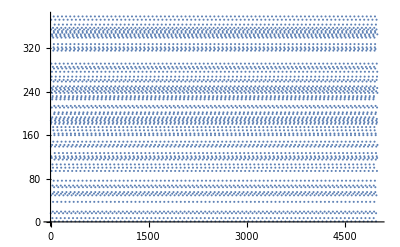

```mathematica
ListPlot[NestList[linearCong,0.0,5000]]
```

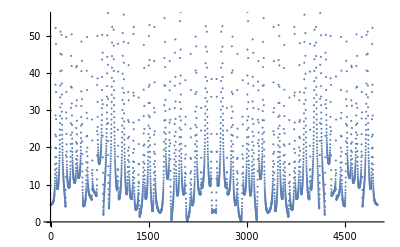

```mathematica
ListPlot[Abs[Fourier[NestList[linearCong,0.0,5000]]]]
```

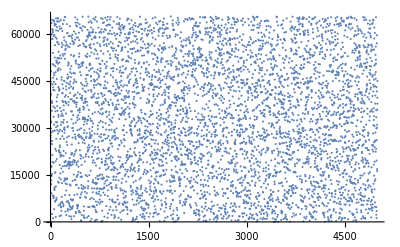

```mathematica
m=2^16;
b=27421;
ListPlot[data=NestList[linearCong,0.0,5000]]
```

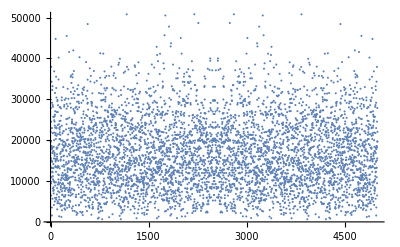

```mathematica
ListPlot[Abs[Fourier[data]]]
```

```mathematica
chiSquare[l_List]:=
Module[{m=Length[l],n=Max[l]},
Sum[(Count[l,i]-m/n)^2,{i,1,n}]/(m/n)]
```

```mathematica
m=381;
b=15;
data=NestList[linearCong,0,1000];
```

```mathematica
chiSquare[data]
```

5018521/1001

```mathematica
N[%]
```

5013.51

```mathematica
m=381;
b=15;
NestList[linearCong,0,100]
```

{0,1,16,241,187,139,181,49,355,373,262,121,292,190,184,94,268,211,118,247,277,346,238,142,226,343,193,229,7,106,67,244,232,52,19,286,100,358,37,175,340,148,316,169,250,322,259,76,379,352,328,349,283,55,64,199,319,214,163,160,115,202,364,127,1,16,241,187,139,181,49,355,373,262,121,292,190,184,94,268,211,118,247,277,346,238,142,226,343,193,229,7,106,67,244,232,52,19,286,100,358}

```mathematica
Position[%,1]
```

{{2},{65}}